```mathematica
{san,bbva}=<<"C:\\Users\\fabregas.TCMM\\Google Drive\\Borsa\\Borsa mat\\Workspace\\stock.mc"
```

{SAN.MC
from  Mon 1 Jan 2007  to  Fri 21 Oct 2016
2557  barsStock Object,BBVA.MC
from  Mon 1 Jan 2007  to  Fri 21 Oct 2016
2557  barsStock Object}

```mathematica
{san,bbva}=<<"C:\\Users\\Joan\\Google Drive\\Borsa\\Borsa mat\\Workspace\\stock.mc"
```

{SAN.MC
from  Mon 1 Jan 2007  to  Fri 21 Oct 2016
2557  barsStock Object,BBVA.MC
from  Mon 1 Jan 2007  to  Fri 21 Oct 2016
2557  barsStock Object}

```mathematica
ssan=san[{2008,1,1},{2008,12,31}]
```

SAN.MC
from  Tue 1 Jan 2008  to  Wed 31 Dec 2008
262  barsStock Object

```mathematica
ma=Strategy["maSF",{100,20}]
```

maSF  {100,20}
 
 Strategy Object

```mathematica
me=Strategy["me",{1}]
```

Strategy::arg: Strategy me not defined

Null

```mathematica
ema=Strategy["Ema Up Down",{20}]
```

Ema Up Down  {20}
 
 Strategy Object

```mathematica
BackTest[ssan,ema]
```

SAN.MC  with  Ema Up Down  {20}
from  Wed 30 Jan 2008  to  Wed 31 Dec 2008
8  tradesBackTest Object

```mathematica
ema20=ema[ssan]
```

{{{2008,1,30},-1},{{2008,1,31},-1},{{2008,2,1},-1},{{2008,2,4},-1},{{2008,2,5},-1},{{2008,2,6},-1},{{2008,2,7},-1},{{2008,2,8},-1},{{2008,2,11},-1},{{2008,2,12},-1},{{2008,2,13},-1},{{2008,2,14},-1},{{2008,2,15},-1},{{2008,2,18},-1},{{2008,2,19},-1},{{2008,2,20},-1},{{2008,2,21},-1},{{2008,2,22},-1},{{2008,2,25},-1},{{2008,2,26},0},{{2008,2,27},1},{{2008,2,28},1},{{2008,2,29},1},{{2008,3,3},-1},{{2008,3,4},-1},{{2008,3,5},-1},{{2008,3,6},-1},{{2008,3,7},-1},{{2008,3,10},-1},{{2008,3,11},-1},{{2008,3,12},-1},{{2008,3,13},0},{{2008,3,14},-1},{{2008,3,17},-1},{{2008,3,18},-1},{{2008,3,19},-1},{{2008,3,20},0},{{2008,3,21},0},{{2008,3,24},1},{{2008,3,25},1},{{2008,3,26},1},{{2008,3,27},1},{{2008,3,28},1},{{2008,3,31},1},{{2008,4,1},1},{{2008,4,2},1},{{2008,4,3},1},{{2008,4,4},1},{{2008,4,7},1},{{2008,4,8},1},{{2008,4,9},1},{{2008,4,10},1},{{2008,4,11},1},{{2008,4,14},1},{{2008,4,15},-1},{{2008,4,16},0},{{2008,4,17},1},{{2008,4,18},1},{{2008,4,21},1},{{2008,4,22},1},{{2008,4,23},1},{{2008,4,24},0},{{2008,4,25},1},{{2008,4,28},1},{{2008,4,29},1},{{2008,4,30},1},{{2008,5,1},1},{{2008,5,2},1},{{2008,5,5},1},{{2008,5,6},1},{{2008,5,7},1},{{2008,5,8},1},{{2008,5,9},1},{{2008,5,12},1},{{2008,5,13},1},{{2008,5,14},1},{{2008,5,15},1},{{2008,5,16},1},{{2008,5,19},1},{{2008,5,20},1},{{2008,5,21},1},{{2008,5,22},-1},{{2008,5,23},-1},{{2008,5,26},-1},{{2008,5,27},-1},{{2008,5,28},-1},{{2008,5,29},-1},{{2008,5,30},-1},{{2008,6,2},-1},{{2008,6,3},-1},{{2008,6,4},-1},{{2008,6,5},-1},{{2008,6,6},-1},{{2008,6,9},-1},{{2008,6,10},-1},{{2008,6,11},-1},{{2008,6,12},-1},{{2008,6,13},-1},{{2008,6,16},-1},{{2008,6,17},-1},{{2008,6,18},-1},{{2008,6,19},-1},{{2008,6,20},-1},{{2008,6,23},-1},{{2008,6,24},-1},{{2008,6,25},-1},{{2008,6,26},-1},{{2008,6,27},-1},{{2008,6,30},-1},{{2008,7,1},-1},{{2008,7,2},-1},{{2008,7,3},-1},{{2008,7,4},-1},{{2008,7,7},-1},{{2008,7,8},-1},{{2008,7,9},-1},{{2008,7,10},-1},{{2008,7,11},-1},{{2008,7,14},-1},{{2008,7,15},-1},{{2008,7,16},-1},{{2008,7,17},-1},{{2008,7,18},-1},{{2008,7,21},0},{{2008,7,22},0},{{2008,7,23},-1},{{2008,7,24},1},{{2008,7,25},1},{{2008,7,28},1},{{2008,7,29},1},{{2008,7,30},0},{{2008,7,31},1},{{2008,8,1},1},{{2008,8,4},1},{{2008,8,5},-1},{{2008,8,6},0},{{2008,8,7},1},{{2008,8,8},1},{{2008,8,11},0},{{2008,8,12},0},{{2008,8,13},1},{{2008,8,14},-1},{{2008,8,15},-1},{{2008,8,18},-1},{{2008,8,19},-1},{{2008,8,20},-1},{{2008,8,21},-1},{{2008,8,22},-1},{{2008,8,25},-1},{{2008,8,26},-1},{{2008,8,27},-1},{{2008,8,28},-1},{{2008,8,29},-1},{{2008,9,1},-1},{{2008,9,2},-1},{{2008,9,3},0},{{2008,9,4},0},{{2008,9,5},-1},{{2008,9,8},-1},{{2008,9,9},0},{{2008,9,10},-1},{{2008,9,11},-1},{{2008,9,12},-1},{{2008,9,15},-1},{{2008,9,16},-1},{{2008,9,17},-1},{{2008,9,18},-1},{{2008,9,19},-1},{{2008,9,22},0},{{2008,9,23},-1},{{2008,9,24},-1},{{2008,9,25},-1},{{2008,9,26},-1},{{2008,9,29},-1},{{2008,9,30},-1},{{2008,10,1},-1},{{2008,10,2},0},{{2008,10,3},-1},{{2008,10,6},0},{{2008,10,7},1},{{2008,10,8},0},{{2008,10,9},-1},{{2008,10,10},-1},{{2008,10,13},-1},{{2008,10,14},-1},{{2008,10,15},-1},{{2008,10,16},-1},{{2008,10,17},-1},{{2008,10,20},-1},{{2008,10,21},-1},{{2008,10,22},-1},{{2008,10,23},-1},{{2008,10,24},-1},{{2008,10,27},-1},{{2008,10,28},-1},{{2008,10,29},-1},{{2008,10,30},-1},{{2008,10,31},-1},{{2008,11,3},-1},{{2008,11,4},-1},{{2008,11,5},-1},{{2008,11,6},-1},{{2008,11,7},-1},{{2008,11,10},-1},{{2008,11,11},-1},{{2008,11,12},-1},{{2008,11,13},-1},{{2008,11,14},-1},{{2008,11,17},-1},{{2008,11,18},-1},{{2008,11,19},-1},{{2008,11,20},-1},{{2008,11,21},-1},{{2008,11,24},-1},{{2008,11,25},-1},{{2008,11,26},-1},{{2008,11,27},-1},{{2008,11,28},-1},{{2008,12,1},-1},{{2008,12,2},-1},{{2008,12,3},-1},{{2008,12,4},-1},{{2008,12,5},-1},{{2008,12,8},-1},{{2008,12,9},0},{{2008,12,10},0},{{2008,12,11},1},{{2008,12,12},1},{{2008,12,15},-1},{{2008,12,16},-1},{{2008,12,17},0},{{2008,12,18},0},{{2008,12,19},1},{{2008,12,22},0},{{2008,12,23},0},{{2008,12,24},0},{{2008,12,25},1},{{2008,12,26},1},{{2008,12,29},1},{{2008,12,30},-1},{{2008,12,31},0}}

```mathematica
fi=FinancialIndicator["ExponentialMovingAverage",20][ssan["OHLCV"]]["Path"];
```

```mathematica
IDateListPlot[{{#[[1]],12+ #[[2]]}&/@ema20,ssan["Low"],fi}]
```

```mathematica
btsan=BackTest[ssan,ma]
```

SAN.MC  with  maSF  {100,20}
from  Wed 21 May 2008  to  Thu 31 Dec 2009
2  tradesBackTest Object

```mathematica
btsan["Performance","Output"->"Table"]
```

Net Return | MDD | Profit Factor | Recovery Factor | Average Trade Return | Winning Trades | Payoff Ratio | Sharpe Ratio | Average Eficiency
-0.0320622 | 34.5172 | 0.968364 | -0.0628401 | -0.00232497 | 0.357143 | 1.74306 | 0.0670678 | -26.311

```mathematica
domain = Flatten[Table[{s,f},{s,100,300,10},{f,10,50,5}],1]
```

```mathematica
opsan=Optimization[san,ma,domain]
```

```mathematica
ListPlot3D[opsan]
```

-Graphics3D-

```mathematica
btsan=BackTest[san,Strategy["maSF",{90,15}]]["Report"]
```

nwb9d_shm29FrontEndObject[LinkObject["nwb9d_shm", 3, 1]]29Untitled-7

```mathematica
btsan2=BackTest[san,ema]
```

SAN.MC  with  Ema Up Down
from  Tue 31 Jul 2007  to  Fri 21 Oct 2016
35  tradesBackTest Object

```mathematica
btsan2["Performance","Output"->"Table"]
```

Net Return | MDD | Profit Factor | Recovery Factor | Average Trade Return | Winning Trades | Payoff Ratio | Sharpe Ratio | Average Eficiency
0.0547648 | 26.339 | 1.05965 | 0.145206 | 0.0015694 | 0.264706 | 2.94347 | 0.0566341 | -31.6516

```mathematica
domain = Table[{s},{s,10,300,10}];
```

```mathematica
opsan2=Optimization[san,ema,domain];
```

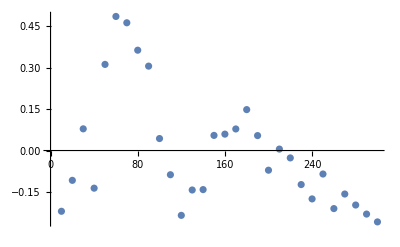

```mathematica
ListPlot[opsan2]
```

```mathematica
btsan=BackTest[san,Strategy["Ema Up Down",{60}]]["Report"]
```

nwb9d_shm31FrontEndObject[LinkObject["nwb9d_shm", 3, 1]]31Untitled-8

```mathematica
backtest1["Performance","Output"->"Table"]
```

Net Return | MDD | Profit Factor | Recovery Factor | Average Trade Return | Winning Trades | Payoff Ratio | Sharpe Ratio | Average Eficiency
0.422686 | 20.6852 | 1.64664 | 1.4851 | 0.0169296 | 0.238095 | 5.26926 | 0.18577 | -22.2979

```mathematica
optimization::arg="The valid options are `1`"
```

The valid options are `1`

```mathematica
Options[optimization]={"Variable"->"Net Return"};
```

```mathematica
optimization[stock_Stock,strategy_Strategy,domain_List,o:OptionsPattern[]]:=
Module[{p=OptionValue["Variable"],n,optima},
Which[
p==="Net Return",n=1,
p==="Maximum Drawdown",n=2,
p==="Profit Factor",n=3,
p==="Recovery Factor",n=4,
p==="Average trade Return",n=5,
p==="Winning Trades",n=6,
p==="Payoff Ratio",n=7,
p==="Sharpe Ratio",n=8,
p=== "Average Efficiency",n=9,
True,
Message[optimization::arg,{"Net Return","Maximum Drawdown","Profit Factor","Recovery Factor","Average trade Return","Winning Trades","Payoff Ratio","Sharpe Ratio","Average Efficiency"}]
];
optima=BackTest[stock,#]["Performance"][[n]]&/@(Strategy[strategy["Name"],#]&/@domain);
MapIndexed[Append[#,optima[[First[#2]]]]&,domain]
]
```

```mathematica
domain = Flatten[Table[{s,f},{s,100,200,20},{f,20,50,10}],1]
```

{{100,20},{100,30},{100,40},{100,50},{120,20},{120,30},{120,40},{120,50},{140,20},{140,30},{140,40},{140,50},{160,20},{160,30},{160,40},{160,50},{180,20},{180,30},{180,40},{180,50},{200,20},{200,30},{200,40},{200,50}}

```mathematica
Dimensions[domain]
```

{24,2}

```mathematica
optimization[bbva,ma,domain]
```

{{100,20,0.127098},{100,30,-0.00829022},{100,40,-0.186621},{100,50,-0.219836},{120,20,-0.108489},{120,30,-0.281093},{120,40,-0.0217447},{120,50,0.040052},{140,20,0.076853},{140,30,-0.127854},{140,40,-0.0237848},{140,50,-0.116689},{160,20,-0.0876283},{160,30,-0.127717},{160,40,-0.269559},{160,50,-0.378123},{180,20,0.0437987},{180,30,-0.152411},{180,40,-0.323343},{180,50,-0.337405},{200,20,0.126283},{200,30,-0.0963616},{200,40,-0.130012},{200,50,-0.185112}}

```mathematica
ListPlot3D[%41]
```

-Graphics3D-

```mathematica
domain=Table[{120+i},{i,0,50,10}]
```

{{120},{130},{140},{150},{160},{170}}

```mathematica
optimization[bbva,strategy1,Table[{120+i},{i,0,50,10}],"Variable"-> "Profit Factor"]
```

{{120,1.14275},{130,1.35106},{140,1.54157},{150,1.64664},{160,1.53903},{170,1.31292}}

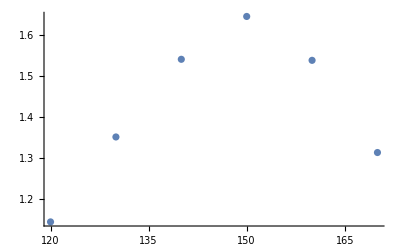

```mathematica
ListPlot[%]
```

```mathematica
MapIndexed[Append[#,op[[First[#2]]]]&,domain]
```

{{100,20,0.127098},{100,30,-0.00829022},{100,40,-0.186621},{100,50,-0.219836},{120,20,-0.108489},{120,30,-0.281093},{120,40,-0.0217447},{120,50,0.040052},{140,20,0.076853},{140,30,-0.127854},{140,40,-0.0237848},{140,50,-0.116689},{160,20,-0.0876283},{160,30,-0.127717},{160,40,-0.269559},{160,50,-0.378123},{180,20,0.0437987},{180,30,-0.152411},{180,40,-0.323343},{180,50,-0.337405},{200,20,0.126283},{200,30,-0.0963616},{200,40,-0.130012},{200,50,-0.185112}}

```mathematica
backtest1["Report"]
```

q77jr_shm50FrontEndObject[LinkObject["q77jr_shm", 3, 1]]50Untitled-5

```mathematica
backtest1["Bootstrap"]
```

q77jr_shm52FrontEndObject[LinkObject["q77jr_shm", 3, 1]]52Untitled-6

```mathematica
optimization[san,strategy1,Table[{50+i},{i,0,250,25}],"Variable"-> "Profit Factor"]
```

{1.17979,1.2019,1.03562,0.805389,1.05965,1.20953,0.903154,0.971438,0.861862,0.721212,0.590632}

```mathematica
Table[{50+i},{i,0,250,25}]
```

{{50},{75},{100},{125},{150},{175},{200},{225},{250},{275},{300}}

```mathematica
par=Strategy["ParabolicStopAndReversal",{0.005,0.5}]
```

ParabolicStopAndReversal  {0.005,0.5}
 
 Strategy Object

```mathematica
td2=BackTest[san,par,"EntryPrices"->{"Median","Medium"},"ExitPrices"->{"Median","Medium"}]
```

SAN.MC  with  ParabolicStopAndReversal
from  Tue 2 Jan 2007  to  Fri 21 Oct 2016
51  tradesBackTest Object

```mathematica
td3=BackTest[bbva,par]
```

BBVA.MC  with  ParabolicStopAndReversal
from  Tue 2 Jan 2007  to  Fri 21 Oct 2016
53  tradesBackTest Object

```mathematica
td2["Report"]
```

kkuxg_shm36FrontEndObject[LinkObject["kkuxg_shm", 3, 1]]36Untitled-10

```mathematica
td2["Performance","Output"-> "Table"]
```

Net Return | MDD | Profit Factor | Recovery Factor | Average Trade Return | Winning Trades | Payoff Ratio | Sharpe Ratio | Average Eficiency
0.410271 | 34.2744 | 1.22734 | 0.864129 | 0.00689932 | 0.4 | 1.84101 | 0.111641 | -15.6076

```mathematica
td3["Report"]
```

mwit5_shm20FrontEndObject[LinkObject["mwit5_shm", 3, 1]]20Untitled-5

```mathematica
td3["Performance"]
```

{2.15556,26.0574,1.86741,2.36168,0.0223454,0.461538,2.17864,0.246146,-2.20901}

```mathematica
td3["Performance","Output"-> "Table"]
```

Net Return | MDD | Profit Factor | Recovery Factor | Average Trade Return | Winning Trades | Payoff Ratio | Sharpe Ratio | Average Eficiency
2.15556 | 26.0574 | 1.86741 | 2.36168 | 0.0223454 | 0.461538 | 2.17864 | 0.246146 | -2.20901

```mathematica
td3["Bootstrap"]
```

mwit5_shm29FrontEndObject[LinkObject["mwit5_shm", 3, 1]]29Untitled-10

```mathematica
td3["Report","Deposit"->{"Simple",5000}]
```

mwit5_shm27FrontEndObject[LinkObject["mwit5_shm", 3, 1]]27Untitled-9

```mathematica
td2["Bootstrap"]
```

kkuxg_shm47FrontEndObject[LinkObject["kkuxg_shm", 3, 1]]47Untitled-12